## Základní návod

Pracovní soubor = zápisník (notebook)

Příkazy se zapisují do buněk (buňky jsou ohraničeny svorkami v pravé části okna)

Buňky mohou mít různý typ (nadpis, podnadpis, text, ...) - lze změnit klepnutím pravým tlačítkem myši na svorku v pravé části okna

Příkazy v buňce typu input se spouštějí SHIFT + Enter (stejně jako v Pythonovském prostředí Jupyter)

Pokud výpočet trvá dlouho, přerušíme ho stiskem ALT + ,

Výpočet probíhá na výpočetních jádrech (kernel) - mohou být lokální i vzdálené

V jedné buňce může být i více příkazů. Musejí být buď každý na nové řádce, nebo odděleny středníkem

Lze exportovat do LaTeXu

Pokud nevíte, jak nějakou funkci použít, stačí na ní najet kurzorem a vyvolat nápovědu stiskem F1

## Použití jako kalkulačka

```mathematica
12+4*7
```

40

```mathematica
12+4 7
```

40

(místo znaku * pro násobení lze použít mezeru)

Faktoriál

```mathematica
15!
```

1307674368000

Mocnina

```mathematica
21^12
```

7355827511386641

Odmocnina

```mathematica
Sqrt[135]
```

3 √15

(Argumenty funkcí se zapisují do hranatých závorek a oddělují čárkou)

Číselná hodnota

```mathematica
Sqrt[135]//N
```

11.619

Číselná hodnota na hodně desetinných míst

```mathematica
N[Pi,1000]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117067982148086513282306647093844609550582231725359408128481117450284102701938521105559644622948954930381964428810975665933446128475648233786783165271201909145648566923460348610454326648213393607260249141273724587006606315588174881520920962829254091715364367892590360011330530548820466521384146951941511609433057270365759591953092186117381932611793105118548074462379962749567351885752724891227938183011949129833673362440656643086021394946395224737190702179860943702770539217176293176752384674818467669405132000568127145263560827785771342757789609173637178721468440901224953430146549585371050792279689258923542019956112129021960864034418159813629774771309960518707211349999998372978049951059731732816096318595024459455346908302642522308253344685035261931188171010003137838752886587533208381420617177669147303598253490428755468731159562863882353787593751957781857780532171226806613001927876611195909216420199

```mathematica
N[Sqrt[2],100]
```

1.414213562373095048801688724209698078569671875376948073176679737990732478462107038850387534327641573

## Speciální symboly a formátování

Mocnina: CTRL + ^

```mathematica
21^12
```

7355827511386641

Odmocnina: CTRL + 2

```mathematica
√4
```

2

n - tá odmocnina CTRL + 2, CTRL + 5

```mathematica
5^(1/3)
```

5^(1/3)

Zlomek : CTRL + /

```mathematica
249/12
```

83/4

Řecké písmeno: ESC, phi, ESC (nebo ESC, f, ESC)

```mathematica
ϕ
```

ϕ

Nekonečno: ESC, inf, ESC

```mathematica
∞
```

∞

Další speciální symboly : ESC, název symbolu, ESC (například imaginární jednotka ESC, ii, ESC)

```mathematica
ⅈ^2
```

-1

(Imaginární jednotka je rovněž označena jako I)

```mathematica
I^2
```

-1

## Proměnné

```mathematica
a=10
```

10

```mathematica
b=√5
```

√5

```mathematica
c=√(a b)
```

√2 5^(3/4)

Zrušení obsahu proměnných

```mathematica
Clear[a,b,c]
```

```mathematica
c
```

c

## Symbolické manipulace

### Práce s výrazy

Pokud proměnné nepřiřadíme hodnotu, lze s ní pracovat jako se symbolem:

```mathematica
v=(x+y+1)^10
```

(1+x+y)^10

Roznásobení závorky

```mathematica
Expand[v]
```

1+10 x+45 x^2+120 x^3+210 x^4+252 x^5+210 x^6+120 x^7+45 x^8+10 x^9+x^10+10 y+90 x y+360 x^2 y+840 x^3 y+1260 x^4 y+1260 x^5 y+840 x^6 y+360 x^7 y+90 x^8 y+10 x^9 y+45 y^2+360 x y^2+1260 x^2 y^2+2520 x^3 y^2+3150 x^4 y^2+2520 x^5 y^2+1260 x^6 y^2+360 x^7 y^2+45 x^8 y^2+120 y^3+840 x y^3+2520 x^2 y^3+4200 x^3 y^3+4200 x^4 y^3+2520 x^5 y^3+840 x^6 y^3+120 x^7 y^3+210 y^4+1260 x y^4+3150 x^2 y^4+4200 x^3 y^4+3150 x^4 y^4+1260 x^5 y^4+210 x^6 y^4+252 y^5+1260 x y^5+2520 x^2 y^5+2520 x^3 y^5+1260 x^4 y^5+252 x^5 y^5+210 y^6+840 x y^6+1260 x^2 y^6+840 x^3 y^6+210 x^4 y^6+120 y^7+360 x y^7+360 x^2 y^7+120 x^3 y^7+45 y^8+90 x y^8+45 x^2 y^8+10 y^9+10 x y^9+y^10

Sdružení podle proměnné y

```mathematica
Collect[v,y]
```

1+10 x+45 x^2+120 x^3+210 x^4+252 x^5+210 x^6+120 x^7+45 x^8+10 x^9+x^10+(10+90 x+360 x^2+840 x^3+1260 x^4+1260 x^5+840 x^6+360 x^7+90 x^8+10 x^9) y+(45+360 x+1260 x^2+2520 x^3+3150 x^4+2520 x^5+1260 x^6+360 x^7+45 x^8) y^2+(120+840 x+2520 x^2+4200 x^3+4200 x^4+2520 x^5+840 x^6+120 x^7) y^3+(210+1260 x+3150 x^2+4200 x^3+3150 x^4+1260 x^5+210 x^6) y^4+(252+1260 x+2520 x^2+2520 x^3+1260 x^4+252 x^5) y^5+(210+840 x+1260 x^2+840 x^3+210 x^4) y^6+(120+360 x+360 x^2+120 x^3) y^7+(45+90 x+45 x^2) y^8+(10+10 x) y^9+y^10

Koeficient u členu x^3

```mathematica
Coefficient[v,x^3]
```

120+840 y+2520 y^2+4200 y^3+4200 y^4+2520 y^5+840 y^6+120 y^7

Faktorizace

```mathematica
Factor[%]
```

120 (1+y)^7

Znak % značí výsledek předchozího výpočtu. Pro výsledek předposledního výpočtu lze použít %%. Pro výsledek 4. výpočtu použijte %4. Výsledek 4. výpočtu je ten, u kterého se objeví Out[4].

```mathematica
Factor[x^2+3x+2]
```

(1+x) (2+x)

### Trigonometrické funkce

```mathematica
v =Tan[x]Cos[2x]
```

Cos[2 x] Tan[x]

Různé goniometrické úpravy

```mathematica
TrigExpand[v]
```

3/2 Cos[x] Sin[x]-Tan[x]/2-1/2 Sin[x]^2 Tan[x]

```mathematica
TrigFactor[v]
```

2 Sin[π/4-x] Sin[π/4+x] Tan[x]

```mathematica
tr=TrigReduce[v]
```

-1/2 Sec[x] (Sin[x]-Sin[3 x])

Operátor nahrazení -> (nahradí uvedenou proměnnou zadanou hodnotou)

```mathematica
tr/.x->π/12
```

-((-1+√3) (-1/(√2)+(-1+√3)/(2 √2)))/(√2)

### Zjednodušování výrazů

Velmi mocné a užitečné. Pozor! Provádění funkce FullSimplify může trvat extrémně dlouho.

```mathematica
Simplify[tr]
```

1/2 Sec[x] (-Sin[x]+Sin[3 x])

```mathematica
FullSimplify[tr]
```

Sin[2 x]-Tan[x]

```mathematica
Simplify[√(x^2),x>0]
```

x

```mathematica
FullSimplify[Cosh[x]-Sinh[x]]
```

ⅇ^-x

### Definice vlastních (uživatelských) funkcí

(namísto = je znak :=; argumenty funkce v deklaraci mají za sebou podtržítko)

```mathematica
f[x_]:=Sin[x^2]
```

```mathematica
f[10]
```

Sin[100]

```mathematica
f[2.1]
```

-0.954628

### Jednoduchý graf

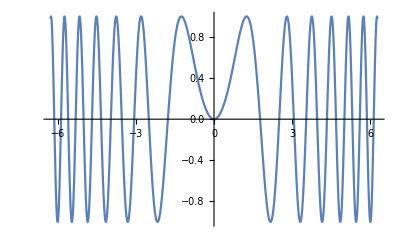

```mathematica
Plot[f[x],{x,-2π,2π}]
```

(Obrázek můžete uložit kliknutím pravým tlačítkem myši a volbou Save Graphic As ...)

### Prostorové a konturové grafy

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2}]
```

-Graphics3D-

(Grafem lze pomocí myši otáčet)

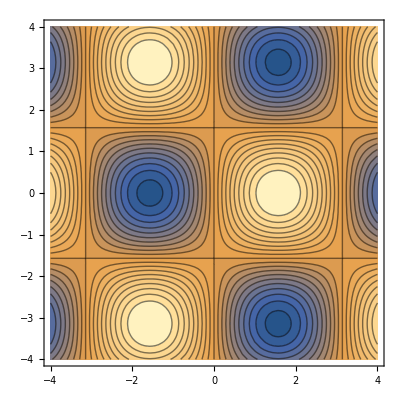

```mathematica
ContourPlot[Sin[x]Cos[y],{x,-4,4},{y,-4,4},Contours->20]
```

### Řešení rovnic a soustav rovnic

Kvadratická rovnice s parametrem

```mathematica
Solve[x^2+ a x-1==0,x]
```

{{x→1/2 (-a-√(4+a^2))},{x→1/2 (-a+√(4+a^2))}}

Rovnice vyššího stupně

```mathematica
Solve[x^4-x^2-5==0,x]
```

{{x→-ⅈ √(1/2 (-1+√21))},{x→ⅈ √(1/2 (-1+√21))},{x→-√(1/2 (1+√21))},{x→√(1/2 (1+√21))}}

```mathematica
N[%,100]
```

{{x→-1.338390020688259616139517499411527391444628008703926859906931522823783809139963728586704693797139445 ⅈ},{x→1.338390020688259616139517499411527391444628008703926859906931522823783809139963728586704693797139445 ⅈ},{x→-1.670714771431054296971980201019601850696331953751988276558403533249566424363147689856682212473735727},{x→1.670714771431054296971980201019601850696331953751988276558403533249566424363147689856682212473735727}}

```mathematica
Solve[x^3+34x+1==0,x]
```

{{x→Root-0.0294Root[1+34 #1+#1^3&,1]-0.029411016448198914},{x→Root0.0147-5.83 ⅈRoot[1+34 #1+#1^3&,2]0.014705508224100362},{x→Root0.0147+5.83 ⅈRoot[1+34 #1+#1^3&,3]0.014705508224100362}}

Diofantovská rovnice

```mathematica
Solve[x^2+2y^3==3681&&x>0 &&y>0,{x,y},Integers]
```

{{x→15,y→12},{x→41,y→10},{x→57,y→6}}

Soustava rovnic s parametrem

```mathematica
Solve[{x^2+y^2==1,x+y==a},{x,y}]
```

{{x→1/2 (a-√(2-a^2)),y→1/2 (a+√(2-a^2))},{x→1/2 (a+√(2-a^2)),y→1/2 (a-√(2-a^2))}}

Nahrazení parametru v posledním výrazem konkrétní hodnotou

```mathematica
%/.a->1
```

{{x→0,y→1},{x→1,y→0}}

### Redukce systému rovnic

```mathematica
Reduce[{2x+3y-5z==1,3x-4y+7z==3},{x,y,z}]
```

y==22-29 x&&z==13-17 x

### Limity

```mathematica
Limit[Sin[x]/x,x->0]
```

1

Následující limitu byste počítali velmi dlouho (L  ' Hospitalovo  pravidlo je nutné použít sedmkrát za sebou)

```mathematica
v=(Sin[Tan[x]]-Tan[Sin[x]])/(ArcSin[ArcTan[x]]-ArcTan[ArcSin[x]])
```

(Sin[Tan[x]]-Tan[Sin[x]])/(ArcSin[ArcTan[x]]-ArcTan[ArcSin[x]])

```mathematica
Limit[v,x->0]
```

1

Taylorova řada čitatele

```mathematica
Series[Numerator[v],{x,0,10}]
```

-x^7/30-(29 x^9)/756+O[x]^11

Taylorova řada jmenovatele

```mathematica
Series[Denominator[v],{x,0,10}]
```

-x^7/30+(13 x^9)/756+O[x]^11

### Řady

Součet konečné řady

```mathematica
Sum[i^2,{i,1,n}]
```

1/6 n (1+n) (1+2 n)

Součet nekonečné řady

```mathematica
Limit[Sum[i^2,{i,1,n}]/(2 n^3+n^2-1),n->Infinity]
```

1/6

```mathematica
Sum[(-1)^(n+1)(x-1)^n/n,{n,1,Infinity}]
```

Log[x]

### Derivování a integrování

```mathematica
D[Cos[3 x^2+2x+1]^3,x]
```

-3 (2+6 x) Cos[1+2 x+3 x^2]^2 Sin[1+2 x+3 x^2]

Druhá (a vyšší derivace)

```mathematica
D[v,{x,2}]
```

-(2 (-1/(√(1-x^2) (1+ArcSin[x]^2))+1/((1+x^2) √(1-ArcTan[x]^2))) (Cos[Tan[x]] Sec[x]^2-Cos[x] Sec[Sin[x]]^2))/(ArcSin[ArcTan[x]]-ArcTan[ArcSin[x]])^2+((2 (-1/(√(1-x^2) (1+ArcSin[x]^2))+1/((1+x^2) √(1-ArcTan[x]^2)))^2)/(ArcSin[ArcTan[x]]-ArcTan[ArcSin[x]])^3-((2 ArcSin[x])/((1-x^2) (1+ArcSin[x]^2)^2)-x/((1-x^2)^(3/2) (1+ArcSin[x]^2))+ArcTan[x]/((1+x^2)^2 (1-ArcTan[x]^2)^(3/2))-(2 x)/((1+x^2)^2 √(1-ArcTan[x]^2)))/(ArcSin[ArcTan[x]]-ArcTan[ArcSin[x]])^2) (Sin[Tan[x]]-Tan[Sin[x]])+(Sec[Sin[x]]^2 Sin[x]-Sec[x]^4 Sin[Tan[x]]+2 Cos[Tan[x]] Sec[x]^2 Tan[x]-2 Cos[x]^2 Sec[Sin[x]]^2 Tan[Sin[x]])/(ArcSin[ArcTan[x]]-ArcTan[ArcSin[x]])

(Volání FullSimplify[%] zde trvá hodiny)

```mathematica
Integrate[x^2 Log[x],x]
```

-x^3/9+1/3 x^3 Log[x]

Určitý integrál

```mathematica
Integrate[Exp[-x^2],{x,0,Infinity}]
```

(√π)/2

### Diferenciální rovnice

Harmonický oscilátor s konkrétní počáteční podmínkou

```mathematica
DSolve[{y''[x]==-y[x],y[0]==0,y'[0]==1},y[x],x]
```

{{y[x]→Sin[x]}}

Složitější lineární diferenciální rovnice (bez zadané počáteční podmínky)

```mathematica
DSolve[y''[x]+2y'[x]+2y[x]==0,y[x],x]
```

{{y[x]→ⅇ^-x C[2] Cos[x]+ⅇ^-x C[1] Sin[x]}}

Ještě složitější rovnice

```mathematica
s=DSolve[{y''[x]+6y'[x]+8y[x]==(2 x^2-2x)Exp[-x],y[0]==3,y'[0]==-6},y[x],x]
```

{{y[x]→1/27 ⅇ^(-4 x) (5+76 ⅇ^(3 x)-66 ⅇ^(3 x) x+18 ⅇ^(3 x) x^2)}}

Vykreslení řešení

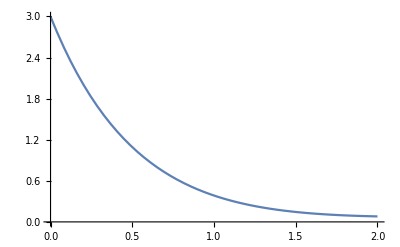

```mathematica
Plot[y[x]/.s,{x,0,2}]
```

### Matice a vektory

Matice (vektory, seznamy) se zapisují pomocí složených závorek

```mathematica
m={{1,h,1},{-h,1,1},{1,1,1}}
```

{{1,h,1},{-h,1,1},{1,1,1}}

```mathematica
m//MatrixForm
```

(1 | h | 1
-h | 1 | 1
1 | 1 | 1)

```mathematica
v=Table[i,{i,1,3}]
```

{1,2,3}

Indexování pomocí [[]], první prvek má index 1

```mathematica
m[[2,1]]
```

-h

Maticové násobení

```mathematica
m.v
```

{4+2 h,5-h,6}

Exponenciála matice

```mathematica
MatrixExp[m]
```

{{-ⅇ/(-2+h^2)-(ⅇ^(1-√(2-h^2)) (1-h^2))/(2 (-2+h^2))-(ⅇ^(1+√(2-h^2)) (1-h^2))/(2 (-2+h^2)),ⅇ/(-2+h^2)-(ⅇ^(1-√(2-h^2)) (1-h √(2-h^2)))/(2 (-2+h^2))-(ⅇ^(1+√(2-h^2)) (1+h √(2-h^2)))/(2 (-2+h^2)),(ⅇ h)/(-2+h^2)-(ⅇ^(1-√(2-h^2)) (h-√(2-h^2)))/(2 (-2+h^2))-(ⅇ^(1+√(2-h^2)) (h+√(2-h^2)))/(2 (-2+h^2))},{ⅇ/(-2+h^2)-(ⅇ^(1+√(2-h^2)) (1-h √(2-h^2)))/(2 (-2+h^2))-(ⅇ^(1-√(2-h^2)) (1+h √(2-h^2)))/(2 (-2+h^2)),-ⅇ/(-2+h^2)-(ⅇ^(1-√(2-h^2)) (1-h^2))/(2 (-2+h^2))-(ⅇ^(1+√(2-h^2)) (1-h^2))/(2 (-2+h^2)),-(ⅇ h)/(-2+h^2)-(ⅇ^(1-√(2-h^2)) (-h-√(2-h^2)))/(2 (-2+h^2))-(ⅇ^(1+√(2-h^2)) (-h+√(2-h^2)))/(2 (-2+h^2))},{-(ⅇ h)/(-2+h^2)-(ⅇ^(1-√(2-h^2)) (-h-√(2-h^2)))/(2 (-2+h^2))-(ⅇ^(1+√(2-h^2)) (-h+√(2-h^2)))/(2 (-2+h^2)),(ⅇ h)/(-2+h^2)-(ⅇ^(1-√(2-h^2)) (h-√(2-h^2)))/(2 (-2+h^2))-(ⅇ^(1+√(2-h^2)) (h+√(2-h^2)))/(2 (-2+h^2)),-(ⅇ^(1-√(2-h^2)))/(-2+h^2)-(ⅇ^(1+√(2-h^2)))/(-2+h^2)+(ⅇ h^2)/(-2+h^2)}}

```mathematica
FullSimplify[%]
```

{{(ⅇ (-1+(-1+h^2) Cosh[√(2-h^2)]))/(-2+h^2),-(ⅇ (-1+Cosh[√(2-h^2)]+h √(2-h^2) Sinh[√(2-h^2)]))/(-2+h^2),(ⅇ (h-h Cosh[√(2-h^2)]-√(2-h^2) Sinh[√(2-h^2)]))/(-2+h^2)},{(ⅇ (1-Cosh[√(2-h^2)]+h √(2-h^2) Sinh[√(2-h^2)]))/(-2+h^2),(ⅇ (-1+(-1+h^2) Cosh[√(2-h^2)]))/(-2+h^2),(ⅇ (-h+h Cosh[√(2-h^2)]-√(2-h^2) Sinh[√(2-h^2)]))/(-2+h^2)},{(ⅇ (-h+h Cosh[√(2-h^2)]-√(2-h^2) Sinh[√(2-h^2)]))/(-2+h^2),(ⅇ (h-h Cosh[√(2-h^2)]-√(2-h^2) Sinh[√(2-h^2)]))/(-2+h^2),(ⅇ (h^2-2 Cosh[√(2-h^2)]))/(-2+h^2)}}

Exponenciála jednotlivých elementů

```mathematica
Exp[m]
```

{{ⅇ,ⅇ^h,ⅇ},{ⅇ^-h,ⅇ,ⅇ},{ⅇ,ⅇ,ⅇ}}

Vlastní hodnoty a vektory

```mathematica
Eigenvalues[m]
```

{1,1-√(2-h^2),1+√(2-h^2)}

```mathematica
Eigenvectors[m]
```

{{1/h,-1/h,1},{-(1-h √(2-h^2))/(-h+√(2-h^2)),-(1-h^2)/(-h+√(2-h^2)),1},{-(-1-h √(2-h^2))/(h+√(2-h^2)),-(-1+h^2)/(h+√(2-h^2)),1}}

Pozor! Oproti jiným programům Mathematica neřadí vlastní čísla podle velikosti a nenormuje vlastní vektory

### Pohybové rovnice

Hamiltonián (kvartický oscilátor)

```mathematica
H[p_,x_]:=p^2/2+x^4
```

Hamiltonovy pohybové rovnice

```mathematica
eq={X'[t]==D[H[p,x],p],P'[t]==-D[H[p,x],x],X[0]==x0,P[0]==p0}/.{x->X[t],p->P[t]}
```

{X'[t]==P[t],P'[t]==-4 X[t]^3,X[0]==x0,P[0]==p0}

Počáteční podmínky s energií E=2

```mathematica
ic=FindInstance[H[p0,x0]==2,{p0,x0},Reals,3]
```

{{p0→-2,x0→0},{p0→-39/76,x0→-(21583/2)^(1/4)/(2 √19)},{p0→-14/19,x0→(2 39^(1/4))/(√19)}}

Řešení pohybové rovnice pro všechny počáteční podmínky 2 (indexuje se pomocí [[2]]) pro čas od 0 do 50

```mathematica
w=NDSolve[eq/.ic[[2]],{X[t],P[t]},{t,50}]
```

{{X[t]→InterpolatingFunction[…][t],P[t]→InterpolatingFunction[…][t]}}

Trajektorie ve fázovém prostoru

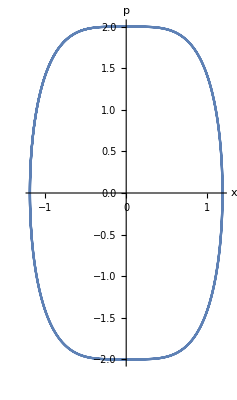

```mathematica
ParametricPlot[Evaluate[{X[t],P[t]}/.w[[1]]],{t,0,10},AxesLabel->{"x","p"}]
```

Souřadnice a hybnost v čase

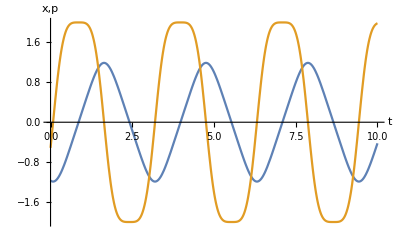

```mathematica
Plot[{Evaluate[X[t]]/.w,Evaluate[P[t]]/.w},{t,0,10},AxesLabel->{"t","x,p"}]
```